### Import Labview-Map and convert to array

```mathematica
SetDirectory[NotebookDirectory[]]
files = FileNames["*.txt"]
```

V:\temp\Hyowon\Spectra

{2_DCmap_hBN-WS2-hBN_4K_25µW_532nm_50x50x1s(30x30V).txt,spec-x4181-y4182.txt}

```mathematica
filename = files⟦1⟧
```

2_DCmap_hBN-WS2-hBN_4K_25µW_532nm_50x50x1s(30x30V).txt

```mathematica
dim = 50;
```

```mathematica
data = Import[filename, "TSV"];
dataohneschrott = data[[7;;1346,;;]];
spec=dataohneschrott[[;;,2;;]];
Dimensions[spec]
wave=dataohneschrott[[;;,1]];
Dimensions[wave]
offset= 98.5;
inttime = 5;
destarray=ConstantArray[0.0,{dim,dim,1340}];
destarray=(Table[spec[[;;,(i+(j-1)*dim)]],{i,1,dim},{j,1,dim}]-offset)/inttime;
(*wavedata=Table[Transpose[{wave,destarray[[a,b,;;1340]]}],{a,1,80},{b,1,80}] ; unten nochmal
Dimensions[wavedata]*)
Dimensions[destarray]
```

{1340,2500}

{1340}

{50,50,1340}

### 2D map-spectral analysis

```mathematica
(*2D-scan-Dynamic-Marker,
Specs= destarray ohne cosmics*)
intensity=destarray;
xticks=Table[Round[0.1*Dimensions[destarray][[1]]-1]*i*j,{i,4},{j,1,2}];
yticks=Table[Round[0.1*Dimensions[destarray][[3]]-1]*i*j,{i,4},{j,1,2}];
wavelength=wave;

Mymax[list_]:=list[[Ordering[list,-1][[1]]]]
SW[list_]:=Dot[list,Range[Length[list]]]/(10*Total[list]+0.01)
```

```mathematica
DynamicModule[{p1={10,10},start=2,stop=Dimensions[intensity]⟦3⟧,marker = 2,min=Max[0,Min[Min[Min[intensity]]]],max=5000,range=50,scalefactor=0.003},
scale=((max-min)/(Exp[scalefactor max]-Exp[scalefactor min]))Exp[scalefactor#]+min-((max-min)/(Exp[scalefactor(max-min)]-1))&;
Grid[{{Grid[{{Grid[{
{"start",Slider[Dynamic[start],{2,Dimensions[intensity]⟦3⟧,1}],Dynamic[wavelength⟦start⟧], "nm"},
{"stop",Slider[Dynamic[stop],{2,Dimensions[intensity]⟦3⟧,1}],Dynamic[wavelength⟦stop⟧],"nm"},
{"marker", Slider[Dynamic[marker], {2, Dimensions[intensity]⟦3⟧,1}], Dynamic[wavelength⟦marker⟧], "nm"},
{"range",Slider[Dynamic[range],{min,max,1}],Dynamic[scale[range]]}}],"    ",SetterBar[Dynamic[func],{Max,Mean,SW}]}}]},{Dynamic[LocatorPane[Dynamic[{p1}],apl=ArrayPlot[Map[func[Take[#,{start,stop}]]&,Reverse[intensity],{2}],PlotRange -> {All,scale[range]}, ImageSize -> Medium,ColorFunction->"Rainbow",PlotLabel->Dynamic["Coordinates: "<>ToString[ Round[{p1[[2]],p1[[1]]}+{0.5,0.5}]]],FrameTicks->{yticks,xticks}]]],Dynamic[Grid[{{lp1 = ListPlot[Transpose[{wavelength,intensity⟦Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5]⟧}],AxesOrigin->{wavelength⟦1⟧-1,0} , GridLines->{{wavelength⟦start⟧,wavelength⟦stop⟧, wavelength⟦marker⟧},{}},AxesStyle-> 20,Joined -> True,PlotRange -> All, ImageSize -> Large]},{N[{Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5]}]}}]]},
{Button["Save Spectrum as PNG", Export["spec-x"<>IntegerString[Round[{Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],1}]]<>"-y"<>IntegerString[Round[{Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],2}]]<>".png", lp1, "PNG"]]},
{Button["Save Spectrum as txt-file", Export["spec-x"<>IntegerString[Round[{Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],1}]]<>"-y"<>IntegerString[Round[{Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],2}]]<>".txt", Transpose[{wavelength,intensity⟦Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5]⟧}], "Table"]]},
{Button["Save Map as PNG", Export["map.png",apl,"PNG"]]},
{Button["Save Map as txt-file", Export["map.txt",Map[func[Take[#,{start,stop}]]&,Reverse[intensity],{2}], "Table"]]}
}]
]
```

```mathematica
+
```

### --energyskala und fitfunktionen--

```mathematica
energy=ConstantArray[0,Dimensions[wave]];
energy=1239.84/wave;
Dimensions[energy]

gaus1[A_, x0_,w_,c_,x_]:=A*Exp[-0.5((x-x0)^2/w^2)]+c;
Totalgaus[a1_,a2_,x01_,x02_,w1_,w2_,x_]:=gaus1[a1,x01,w1,0,x]+gaus1[a2,x02,w2,0,x];
Dreiergauß[a1_,a2_,a3_,x01_,x02_,x03_,w1_,w2_,w3_,x_]:=gaus1[a1,x01,w1,0,x]+gaus1[a2,x02,w2,0,x]+gaus1[a3,x03,w3,0,x];
maparray=ConstantArray[0, {Dimensions[destarray][[1]],Dimensions[destarray][[2]]}];
```

{1340}

### Single-pixel-fit

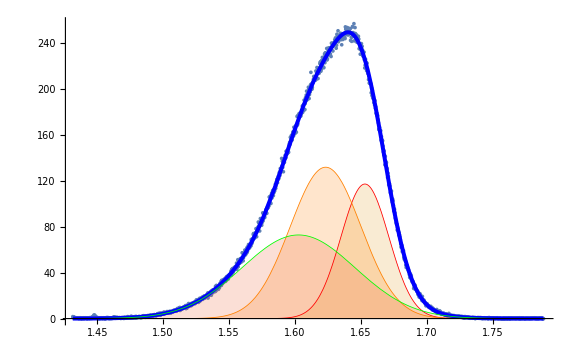

| Estimate | Standard Error | t-Statistic | P-Value
a1 | 117.212 | 12.5347 | 9.35104 | 3.54716×10^-20
a2 | 131.853 | 10.64 | 12.3923 | 1.86321×10^-33
a3 | 72.839 | 4.64276 | 15.6887 | 5.01181×10^-51
x01 | 1.6531 | 0.000359003 | 4604.69 | 5.52264684786×10^-2799
x02 | 1.62332 | 0.00203798 | 796.531 | 2.36673298234×10^-1785
x03 | 1.60272 | 0.00131084 | 1222.66 | 1.04380402582×10^-2032
w1 | 0.0182102 | 0.000409769 | 44.4402 | 3.17507×10^-265
w2 | 0.0269302 | 0.00123715 | 21.7679 | 4.06874×10^-90
w3 | 0.0430238 | 0.00027197 | 158.193 | 2.48859198472×10^-865

{5.3503,8.90063,7.85496}

{0.0428818,0.0634159,0.101313}

```mathematica
(*DEFINIERE SINGLE_PIXEL*)
{picx,picy}={35,34};
destdata=Transpose[{energy,destarray[[picx,picy,;;1340]]}] ;
If[
Max[destarray[[picx,picy,;;1340]]]>100,
harterfit=NonlinearModelFit[destdata,{Dreiergauß[a1,a2,a3,x01,x02,x03,w1,w2,w3,x]},{{a1,62},{a2,76},{a3,36},{x01,1.65},{x02,1.62},{x03,1.56},{w1,0.013},{w2,0.037},{w3,0.066}},x];
harterfit["BestFitParameters"];
{ga1,ga2,ga3,gx1,gx2,gx3,gw1,gw2,gw3}={a1,a2,a3,x01,x02,x03,w1,w2,w3}/.harterfit["BestFitParameters"];


Show[
ListPlot[destdata],
Plot[{harterfit[x],gaus1[ga1,gx1,gw1,0,x],gaus1[ga2,gx2,gw2,0,x],gaus1[ga3,gx3,gw3,0,x]},{x,Min[energy],Max[energy]},PlotRange->All,PlotStyle->{ {Blue,Thickness[0.005]},{Red, Thickness[0.001]},{Orange, Thickness[0.001]},{Green,Thickness[0.001]}}, Filling->{1->None,2->Axis,3->Axis,4->Axis},ImageSize->Large],

PlotRange->All,ImageSize->Large]


,
Show[ListPlot[destdata],PlotRange->All ]
]
parameterarray=harterfit["ParameterTable"]
{intval1,intval2,intval3}=Integrate[{gaus1[ga1,gx1,gw1,0,x],gaus1[ga2,gx2,gw2,0,x],gaus1[ga3,gx3,gw3,0,x]},{x,Min[energy],Max[energy]}]

{fwhm1,fwhm2,fwhm3}=Abs[2Sqrt[2*Log[2]]*{gw1,gw2,gw3}]
```

### Map-Fit

```mathematica
Mapfitdata={};
treshholdintIntensity=10000;
(*Change spectral fit area in destdata and for thresholdvalue in destarray*)
For[i=1,i≤Dimensions[destarray][[1]],i++,
For[j=1,j≤Dimensions[destarray][[2]],j++,
If[Total[destarray[[i,j,;;1340]]]>treshholdintIntensity,
destdata=Transpose[{energy[[;;]],destarray[[i,j,;;]]}] ;
(*mapfit=NonlinearModelFit[destdata,Totalgaus[a1,a2,x01,x02,w1,w2,x],{{a1,500},{a2,500},{x01,750},{x02,800},w1,w2},x];*)
mapfit=NonlinearModelFit[destdata,Dreiergauß[a1,a2,a3,x01,x02,x03,w1,w2,w3,x],{{a1,62},{a2,76},{a3,36},{x01,1.65},{x02,1.62},{x03,1.56},{w1,0.013},{w2,0.037},{w3,0.066}},x];
(*harterfit["BestFitParameters"];
{ga1,ga2,ga3,gx1,gx2,gx3,gw1,gw2,gw3}={a1,a2,a3,x01,x02,x03,w1,w2,w3}/.harterfit["BestFitParameters"];*)

parameterarray=mapfit["ParameterTableEntries"];
ninepar=parameterarray[[;;,1]];
{int1,int2,int3}=Integrate[{gaus1[a1,x01,w1,0,x],gaus1[a2,x02,w2,0,x],gaus1[a3,x03,w3,0,x]},{x,Min[energy],Max[energy]}]/.mapfit["BestFitParameters"];
{fwhm1,fwhm2,fwhm3}=2Sqrt[2*Log[2]]*{w1,w2,w3}/.mapfit["BestFitParameters"];
(*peak1=FindArgMax[gaus1[ga1,gx1,gw1,0,x],{x,Min[energy],Max[energy]}][[1]];
peak2=FindArgMax[gaus1[ga2,gx2,gw2,0,x],{x,Min[energy],Max[energy]}][[1]];
peak3=FindArgMax[gaus1[ga3,gx3,gw3,0,x],{x,Min[energy],Max[energy]}][[1]];
diffpeak12=peak2-peak1;
divpeakint12=int1/int2;*)
Mapfitdata=Append[Mapfitdata,{i,j,ninepar,{int1,int2,int3},{fwhm1,fwhm2,fwhm3}}];
,(*else*)
Mapfitdata=Append[Mapfitdata,{i,j,{0,0,0,0,0,0,0,0,0},{0,0,0},{0,0,0}}];

];
If[mapfit=={}, maparray[[i,j]]=0, maparray[[i,j]]=1];

]]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

### Evaluate destdata-format (posx-posy-fitparameters[9-see-table-]-IntI[3]-FWHM[3]) "" | "Estimate" | "Standard Error" | "t-Statistic" | "P-Value" a1 | 120.181 | 0.734388 | 163.647 | 5.73414799627×10^-884 a2 | 119.625 | 2.24805 | 53.2129 | 7.50714988711×10^-332 a3 | 52.1301 | 1.20855 | 43.1342 | 4.8209×10^-255 x01 | 1.65388 | 0.0000553654 | 29872. | 7.98871355932×10^-3880 x02 | 1.62809 | 0.000241588 | 6739.13 | 3.98180966819×10^-3019 x03 | 1.57119 | 0.00203543 | 771.922 | 2.99025927904×10^-1767 w1 | 0.0135554 | 0.0000743189 | 182.396 | 5.50571479272×10^-944 w2 | 0.0359647 | 0.000294856 | 121.974 | 8.16020043463×10^-725 w3 | 0.0620797 | 0.000766897 | 80.9491 | 1.75505314366×10^-516

```mathematica
(*Export 2d array as txt with parameters specified in Mapdata*)
Button["Export 2D array with fitdata"Export["X-map-SiO-WSe-300K.txt",Partition[Mapfitdata⟦All,3,1⟧,80],"Table"]]
```

Export 2D array with fitdata X-map-SiO-WSe-300K.txt

```mathematica
(*convert data to array*)
fitarray=ConstantArray[0.0,{80,80,5}];
fitarray=Table[Mapfitdata[[j+(i-1)*80,;;]],{i,1,80},{j,1,80}];
Dimensions[fitarray]
```

{80,80,5}

```mathematica
fitarray[[35,34,;;]]
```

{35,34,{117.212,131.853,72.839,1.6531,1.62332,1.60272,0.0182102,0.0269302,0.0430238},{5.3503,8.90063,7.85496},{0.0428818,0.0634159,0.101313}}

### Recontruct fits with array

```mathematica
(*fit1= gaus1[fitarray[[i,j,3,1]],fitarray[[i,j,3,4]],fitarray[[i,j,3,7]],0,x];
fit2=gaus1[fitarray[[i,j,3,2]],fitarray[[i,j,3,5]],fitarray[[i,j,3,8]],0,x];
fit3=gaus1[fitarray[[i,j,3,3]],fitarray[[i,j,3,6]],fitarray[[i,j,3,9]],0,x];
fullfit= fit1+fit2+fit3;*)
```

### manipulate-map

```mathematica
Manipulate[
If[fitarray[[i,j,3,1]]≠0,
fit1= gaus1[fitarray[[i,j,3,1]],fitarray[[i,j,3,4]],fitarray[[i,j,3,7]],0,x];
fit2=gaus1[fitarray[[i,j,3,2]],fitarray[[i,j,3,5]],fitarray[[i,j,3,8]],0,x];
fit3=gaus1[fitarray[[i,j,3,3]],fitarray[[i,j,3,6]],fitarray[[i,j,3,9]],0,x];
fullfit= fit1+fit2+fit3;
(*Convert fits from fitplots in a Table, stepsize=deleV(energyscale)/1340*)
Datafitplots=Table[{x,fit1,fit2,fit3,fullfit},{x,Min[energy],Max[energy],0.000266574626865671}];
fitgausanddata=Show[

ListPlot[Transpose[{energy,destarray[[i,j,;;1340]]}],ImageSize->Large],
fitplots=Plot[{
fullfit,
fit1,
fit2,
fit3}
,{x,Min[energy],Max[energy]},PlotRange->All,ImageSize->Large]
]

Button["export fit-data-eV",Export["fitplots-mathematica.txt",Datafitplots,"Table"]]Button["export raw-data",Export["fitplots-rawdata-mathematica.txt", Reverse[Transpose[{energy,destarray[[i,j,;;1340]]}]],
"Table"]]
(*werte={fitarray[[i,j,5,1]],fitarray[[i,j,5,2]],fitarray[[i,j,5,3]]}*)

,
{};
]
,{i,1,80,1},{j,1,80,1}]
```

```mathematica
fitarray[[22,16,5,1]]
fitarray[[22,16,5,2]]
fitarray[[22,16,5,3]]
fitarray[[22,16,3,4]]
fitarray[[22,16,3,5]]
fitarray[[22,16,3,6]]
```

-0.0353832

0.0560264

0.0900355

1.65916

1.64185

1.62654

```mathematica
(*2D-scan-Dynamic-Marker,
Specs= destarray ohne cosmics*)
intensity=destarray;
xticks=Table[Round[0.1*Dimensions[destarray][[1]]-1]*i*j,{i,4},{j,1,2}];
yticks=Table[Round[0.1*Dimensions[destarray][[3]]-1]*i*j,{i,4},{j,1,2}];
wavelength=wave;

Mymax[list_]:=list[[Ordering[list,-1][[1]]]]
SW[list_]:=Dot[list,Range[Length[list]]]/(10*Total[list]+0.01)
```

```mathematica
DynamicModule[{p1={10,10},start=2,stop=Dimensions[intensity]⟦3⟧,marker = 2,min=Max[0,Min[Min[Min[intensity]]]],max=5000,range=50,scalefactor=0.003},
scale=((max-min)/(Exp[scalefactor max]-Exp[scalefactor min]))Exp[scalefactor#]+min-((max-min)/(Exp[scalefactor(max-min)]-1))&;
Grid[{{Grid[{{Grid[{
{"start",Slider[Dynamic[start],{2,Dimensions[intensity]⟦3⟧,1}],Dynamic[wavelength⟦start⟧], "nm"},
{"stop",Slider[Dynamic[stop],{2,Dimensions[intensity]⟦3⟧,1}],Dynamic[wavelength⟦stop⟧],"nm"},
{"marker", Slider[Dynamic[marker], {2, Dimensions[intensity]⟦3⟧,1}], Dynamic[wavelength⟦marker⟧], "nm"},
{"range",Slider[Dynamic[range],{min,max,1}],Dynamic[scale[range]]}}],"    ",SetterBar[Dynamic[func],{Max,Mean,SW}]}}]},{Dynamic[LocatorPane[Dynamic[{p1}],apl=ArrayPlot[Map[func[Take[#,{start,stop}]]&,Reverse[intensity],{2}],PlotRange -> {All,scale[range]}, ImageSize -> Medium,ColorFunction->"Rainbow",PlotLabel->Dynamic["Coordinates: "<>ToString[ Round[{p1[[2]],p1[[1]]}+{0.5,0.5}]]],FrameTicks->{yticks,xticks}]]],Dynamic[Grid[{{Show[

ListPlot[Transpose[{energy,destarray[[Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],;;1340]]}],ImageSize->Large],
fitplots=Plot[{
gaus1[fitarray[[Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],3,1]],fitarray[[Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],3,4]],fitarray[[Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],3,7]],0,x]+
gaus1[fitarray[[Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],3,2]],fitarray[[Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],3,5]],fitarray[[Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],3,8]],0,x]+
gaus1[fitarray[[Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],3,3]],fitarray[[Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],3,6]],fitarray[[Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],3,9]],0,x],
gaus1[fitarray[[Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],3,1]],fitarray[[Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],3,4]],fitarray[[Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],3,7]],0,x],
gaus1[fitarray[[Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],3,2]],fitarray[[Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],3,5]],fitarray[[Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],3,8]],0,x],
gaus1[fitarray[[Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],3,3]],fitarray[[Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],3,6]],fitarray[[Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],3,9]],0,x]}
,{x,Min[energy],Max[energy]},PlotRange->All,ImageSize->Large]
]
(*lp1 = ListPlot[Transpose[{wavelength,intensity⟦Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5]⟧}],AxesOrigin->{wavelength⟦1⟧-1,0} , GridLines->{{wavelength⟦start⟧,wavelength⟦stop⟧, wavelength⟦marker⟧},{}},AxesStyle-> 20,Joined -> True,PlotRange -> All, ImageSize -> Large]*)},{N[{Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5]}]}}]]},
{Button["Save Spectrum as PNG", Export["spec-x"<>IntegerString[Round[{Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],1}]]<>"-y"<>IntegerString[Round[{Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],2}]]<>".png", lp1, "PNG"]]},
{Button["Save Spectrum as txt-file", Export["spec-x"<>IntegerString[Round[{Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],1}]]<>"-y"<>IntegerString[Round[{Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5],2}]]<>".txt", Transpose[{wavelength,intensity⟦Round[p1⟦2⟧+.5],Round[p1⟦1⟧+.5]⟧}], "Table"]]},
{Button["Save Map as PNG", Export["map.png",apl,"PNG"]]},
{Button["Save Map as txt-file", Export["map.txt",Map[func[Take[#,{start,stop}]]&,Reverse[intensity],{2}], "Table"]]}
}]
]
```